# Project Euler Problem 91

Plenty of room for optimization here!

```mathematica
rightTriangleQ[v1_, v2_] := v1 ≠ v2 ≠ {0, 0} && (v1.v2 == 0 || v1.(v2-v1) == 0 || v2.(v1-v2) == 0)
```

```mathematica
drawTriangle[v1_, v2_, M_] := Graphics[Triangle[{{0, 0}, v1, v2}],
	ImageSize -> {200,200},
	PlotRange -> {{0, M}, {0, M}},
	GridLines -> {Range[0, M], Range[0, M]}
]
```

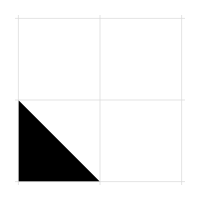
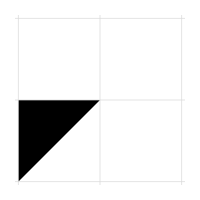
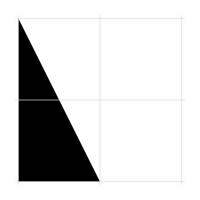
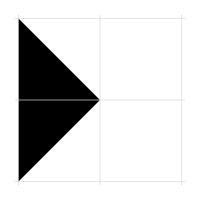
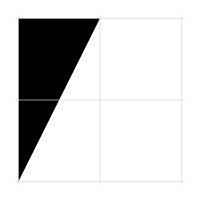
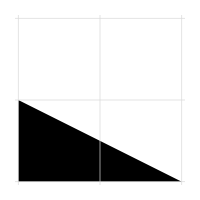
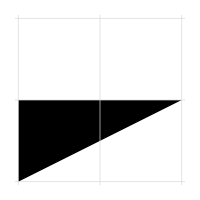
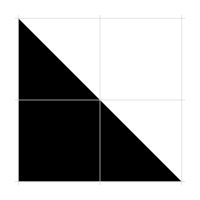
n = 1 | -Graphics-
n = 2 | -Graphics-
n = 3 | -Graphics-
n = 4 | -Graphics-
n = 5 | -Graphics-
n = 6 | -Graphics-
n = 7 | -Graphics-
n = 8 | -Graphics-
n = 9 | -Graphics-
n = 10 | -Graphics-
n = 11 | -Graphics-
n = 12 | -Graphics-
n = 13 | -Graphics-
n = 14 | -Graphics-
n = 15 | -Graphics-
n = 16 | -Graphics-
n = 17 | -Graphics-
n = 18 | -Graphics-
n = 19 | -Graphics-
n = 20 | -Graphics-
n = 21 | -Graphics-
n = 22 | -Graphics-
n = 23 | -Graphics-
n = 24 | -Graphics-
n = 25 | -Graphics-
n = 26 | -Graphics-
n = 27 | -Graphics-
n = 28 | -Graphics-

```mathematica
Module[{M = 2, n = 0},
	Grid[Partition[Flatten[
		Table[If[rightTriangleQ[{x1, y1}, {x2, y2}], {"n = " <> ToString[++n], drawTriangle[{x1, y1}, {x2, y2}, M]}, Nothing], {x1, 0, M}, {x2, 0, M}, {y1, 0, M}, {y2, 0, M}]
	], 2]]
]
```

```mathematica
Module[{M = 50, n = 0},
	Do[If[rightTriangleQ[{x1, y1}, {x2, y2}], ++n], {x1, 0, M}, {x2, 0, M}, {y1, 0, M}, {y2, 0, M}];
	n / 2
]
```

14234